# Sang' s sample data set analysis

### 2020 - 05 - 25 Minho Kwon

#### Import the dataset

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["d1.csv"];
```

#### Print out the data

```mathematica
xdata=data[[2;;,2]]
ydata=data[[2;;,3]]
zdata=data[[2;;,4]]
tdata=data[[2;;,5]]
```

{0.327778,0.244444,-0.00555556,0.0777778,-0.00555556,-0.422222,0.327778,-0.172222,-0.00555556,-0.255556,-0.255556,-0.00555556,-0.00555556,-0.255556,-0.172222,-0.172222,0.161111,0.244444,-0.0888889,0.161111,0.161111,-0.422222,-0.00555556,0.0777778,-0.172222,0.327778,-0.00555556,-0.0888889,0.244444}

{-0.0275862,-0.0275862,-0.227586,-0.227586,0.272414,0.0724138,0.0724138,-0.0275862,0.0724138,-0.127586,-0.0275862,-0.127586,0.0724138,0.0724138,0.172414,-0.127586,0.172414,0.272414,-0.127586,-0.127586,0.272414,0.0724138,0.0724138,-0.427586,-0.0275862,-0.127586,-0.227586,0.272414,0.0724138}

{-0.0866667,-0.186667,-0.386667,0.113333,0.213333,0.313333,-0.386667,-0.0866667,0.113333,-0.186667,-0.0866667,0.213333,0.0133333,-0.0866667,0.313333,0.113333,0.113333,-0.286667,-0.186667,-0.0866667,0.0133333,0.213333,0.0133333,0.0133333,-0.386667,0.0133333,0.213333,0.313333,-0.0866667}

{0.283636,0.147273,0.192727,0.0290909,-0.189091,-0.361818,0.0563636,0.0472727,-0.08,0.201818,-0.0709091,0.0654545,-0.270909,-0.207273,-0.143636,-0.0618182,0.0745455,-0.316364,0.0927273,0.0836364,0.347273,0.0109091,0.0836364,-0.325455,-0.270909,0.229091,0.310909,-0.189091,0.247273}

#### Correlation between X and Z

FittedModel[-0.00913168-0.319565 x]

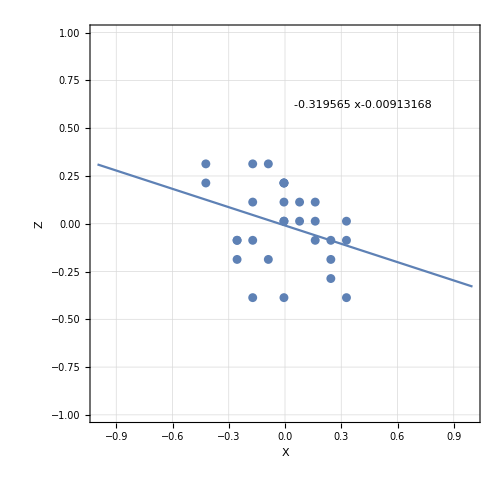

```mathematica
fitxz=NonlinearModelFit[Transpose[{xdata,zdata}],a x+b,{a,b},x]
Show[ListPlot[Transpose[{xdata,zdata}]],Plot[fitxz[x],{x,-1,1},PlotLegends->Placed[Text[fitxz[x]],{0.7,0.8}]],Frame->True,FrameLabel->{"X","Z"},ImageSize->500,LabelStyle->FontSize->20,GridLines->Automatic,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]
```

Constructing a nonlinear model

#### Values can be thought as mathematical distance in n-dimensional vector space. Therefore it makes sense to limit the order up to quadratic. For example, x^2, y^2, z^2, and cross-terms xy, yz and xz. Coefficients for the cross-terms will vanish if they were completely independent.

```mathematica
fitxyzTot=NonlinearModelFit[Transpose[{xdata,ydata,zdata,tdata}],a x+b y+ c z+d x y + e y z + f x z+g x^2+h y^2+i z^2,{a,b,c,d,e,f,g,h,i},{x,y,z}]
(*fitxyzTot=NonlinearModelFit[{xdata,ydata,zdata,tdata}^ᵀ,a x+b y+ c z+g x^2+h y^2+i z^2,{a,b,c,g,h,i},{x,y,z}]*)
(*fitxyzTot=NonlinearModelFit[{xdata,ydata,zdata,tdata}^ᵀ,a x+b y+ c z,{a,b,c},{x,y,z}]*)
(*fitxyzTot=NonlinearModelFit[{xdata,ydata,zdata,tdata}^ᵀ,a x+b y,{a,b},{x,y,z}]*)
(*fitxyzTot=NonlinearModelFit[{xdata,ydata,zdata,tdata}^ᵀ,a x,{a},{x,y,z}]*)
(*fitxyzTot=NonlinearModelFit[{xdata,ydata,zdata,tdata}^ᵀ,b y,{b},{x,y,z}]*)
```

#### Fitted model

```mathematica
fitxyzTot["ParameterTable"]
fitxyzTot[x,y,z]
Print["Tdata predicted from x,y,z inputs"]
fitteddata=Table[fitxyzTot[xdata[[i]],ydata[[i]],zdata[[i]]],{i,1,Length[xdata]}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.706329 | 0.170893 | 4.13317 | 0.000515261
b | -0.783049 | 0.236231 | -3.31476 | 0.00345725
c | 0.520554 | 0.220658 | 2.3591 | 0.0286018
d | 5.69107 | 1.81301 | 3.13901 | 0.00516632
e | 3.0136 | 1.14528 | 2.63131 | 0.0160034
f | 1.1142 | 0.980478 | 1.13639 | 0.269228
g | 1.71758 | 0.631378 | 2.72037 | 0.0131765
h | -2.17941 | 0.756488 | -2.88096 | 0.00923807
i | -0.275267 | 0.735538 | -0.374239 | 0.712165

0.706329 x+1.71758 x^2-0.783049 y+5.69107 x y-2.17941 y^2+0.520554 z+1.1142 x z+3.0136 y z-0.275267 z^2

Tdata predicted from x,y,z inputs

{0.312908,0.114771,0.0938058,0.017468,-0.115192,-0.177112,0.0149703,-0.0470672,0.00519881,0.199817,-0.0235693,0.0797701,-0.0645735,-0.2832,-0.200724,0.108916,0.251362,-0.206049,0.0632559,0.0764096,0.0533402,-0.189448,-0.0645735,-0.196714,-0.159814,0.249117,0.0195398,-0.199788,0.218196}

#### How well that prediction matches to Tdata?

```mathematica
Print["Correlation:"<>ToString[Correlation[fitteddata,tdata]]]
```

Correlation:0.781726

#### Visualization : Predictor (or estimator?) from (X,Y,Z) versus Tdata

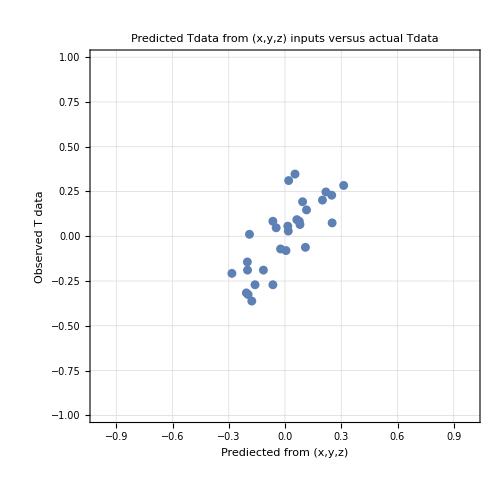

0.128225

```mathematica
ListPlot[Transpose[{fitteddata,tdata}],Frame->True,FrameLabel->{"Prediected from (x,y,z)","Observed T data"},LabelStyle->FontSize->24,ImageSize->500,AspectRatio->1,GridLines->Automatic,PlotRange->{{-1,1},{-1,1}},PlotLabel->"Predicted Tdata from (x,y,z) inputs \n versus actual Tdata"]
StandardDeviation[tdata-fitteddata]
```